JSON Import

```mathematica
OpenJSONDialog[]:=SystemDialogInput["FileOpen",{"simdata.json",{"RiverSim files"->{"*.json"}}}]
```

```mathematica
ImportJSONData[files_]:=Module[{},
Switch[Head[files],
String,
Import[files,"RawJSON"],
List,
Import[#,"RawJSON"]&/@files
]
];
OpenJSONData[]:=Module[{files},
files=OpenJSONDialog[];
ImportJSONData[files]
];
```

Visualize and process input JSON

### Plots simulation data structure. Single or list of simulations data

```mathematica
plotSimData[data_, color_:RGBColor[0.368417, 0.506779, 0.709798],legend_:"" ]:=
ListPlot[
Flatten[data["Trees"]["Branches"][[All,"coords"]],{1}],
Joined->True,
PlotRange->{{0,(*data["Model", "width"]*)2},{0,(*data["Model", "height"]*)5.5}}, 
AspectRatio->1, 
PlotStyle->color,
(*PlotLegends->{legend},*)
AxesLabel->{"X","Y"}];
```

```mathematica
plotJSON[filePath_]:=
plotSimData[Import[filePath, "RawJSON"]];
```

Cut and compare rivers

```mathematica
cutRivers[data_, fileName_]:=Module[{initialDistance,toDrop,dataExport},
initialDistance = EuclideanDistance[#1,#2]&@@data["Trees","Branches"][[All,2,1]];
toDrop=Count[MapThread[EuclideanDistance,data["Trees","Branches"][[All,2]]],u_/;u>3initialDistance];
dataExport=data;
dataExport[[6,1,All,2]]=Drop[#,-toDrop]&/@data["Trees","Branches"][[All,2]];
Export[NotebookDirectory[]<>fileName,dataExport];
dataExport]
```

```mathematica
compare15[datas_]:=Module[{savedOpt=Options[ListPlot],pr={{0,2},{0,5.5}}, ar=2},
SetOptions[ListPlot,PlotRange->pr,AspectRatio->ar,Joined->True,PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.560181, 0.691569, 0.194885]}];
Print@GraphicsRow[{
ListPlot[Flatten[{Flatten[datas[[1,6,1,All,2]],{1}],Flatten[datas[[2,6,1,All,2]],{1}],Flatten[datas[[3,6,1,All,2]],{1}]},1]],
ListPlot[Flatten[{Flatten[datas[[4,6,1,All,2]],{1}],Flatten[datas[[5,6,1,All,2]],{1}],Flatten[datas[[6,6,1,All,2]],{1}]},1]],
ListPlot[Flatten[{Flatten[datas[[7,6,1,All,2]],{1}],Flatten[datas[[8,6,1,All,2]],{1}],Flatten[datas[[9,6,1,All,2]],{1}]},1]],
ListPlot[Flatten[{Flatten[datas[[10,6,1,All,2]],{1}],Flatten[datas[[11,6,1,All,2]],{1}],Flatten[datas[[12,6,1,All,2]],{1}]},1]],
ListPlot[Flatten[{Flatten[datas[[13,6,1,All,2]],{1}],Flatten[datas[[14,6,1,All,2]],{1}],Flatten[datas[[15,6,1,All,2]],{1}]},1]]},ImageSize->1200];
SetOptions[ListPlot,savedOpt];]
```

```mathematica
datas=OpenJSONData[];
```

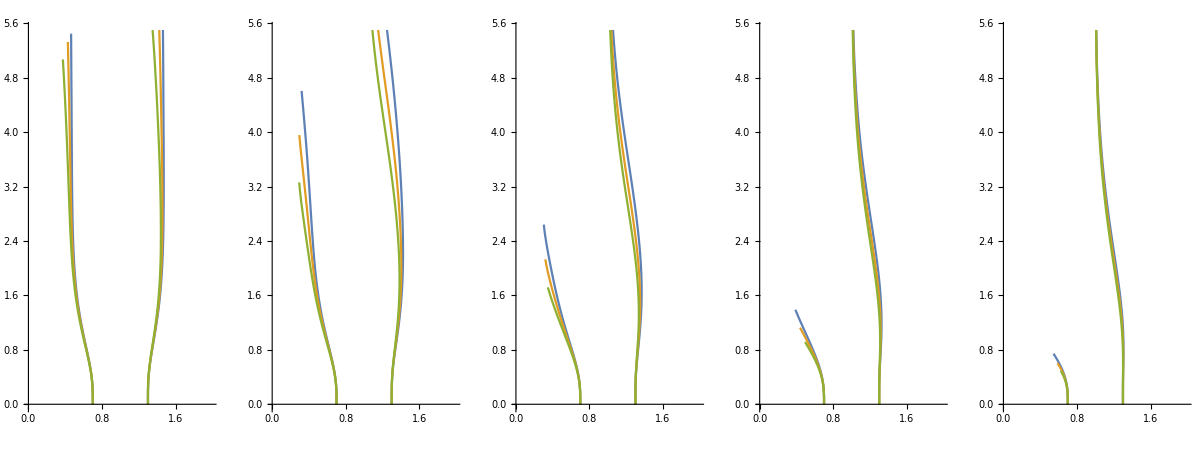

```mathematica
compare15[datas]
```

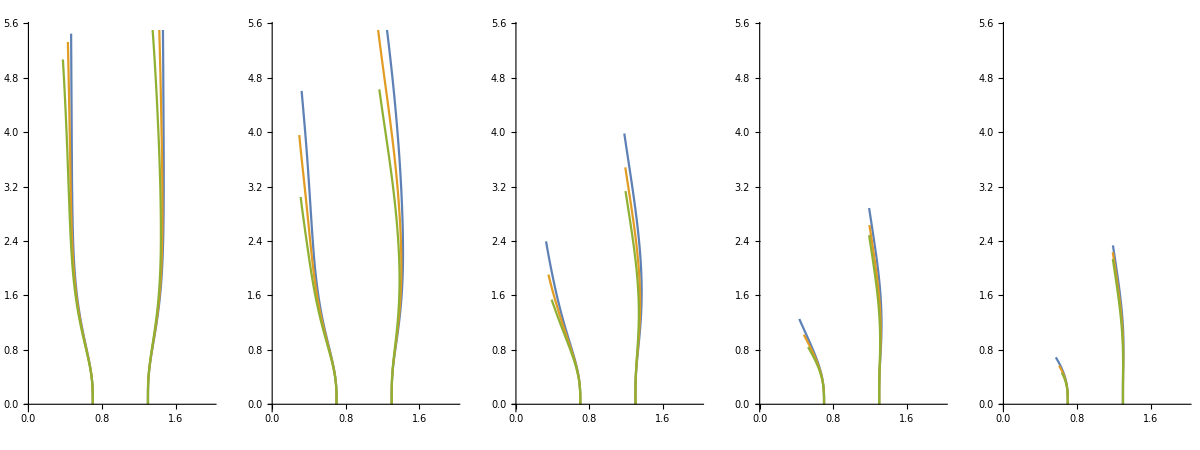

```mathematica
datasExport=MapThread[cutRivers,{datas,Table["initialLength1/cut_rivers/lap"<>ToString[index]<>".json",{index,Range@Length@datas}]}];compare15[datasExport]
```